Piecewise[{{1-x^(3/2), x<1}, {0, True}}]

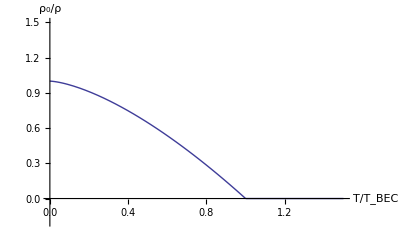

```mathematica
Clear[f]
f[x_] = Piecewise[{{1 - x^(3/2), x < 1}, {0, x≥ 1}}]
Plot[f[x], {x, 0, 1.5}, PlotRange -> {{0, 1.5}, {-0.2, 1.5}},
AxesLabel->{T/Subscript[T, BEC], Subscript[ρ, 0]/ρ}
]
```

```mathematica
$Assumptions = β > 0 ;
i = Integrate[ϵ^3/(E^(ϵ β)-1), {ϵ, 0, Infinity}] ;
i // TraditionalForm
```

π^4/(15 β^4)